```mathematica
sol[n_]:=Module[{plane={},points={}},points = Flatten[Table[{i,j},{i,1,4},{j,1,4}],1];
For[i=1,i≤Length[points],i++,
If[points[[i]][[1]]+points[[i]][[2]]==n && Length[Union[points[[i]]]]==2,AppendTo[plane,points[[i]]]]];
Return[plane]
]
```

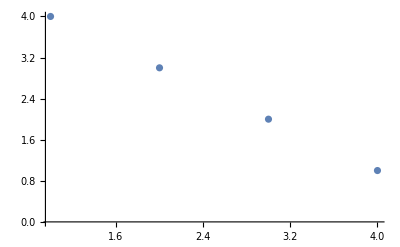

```mathematica
ListPlot[sol[5]]
```

```mathematica
sol[n_]:=Module[{plane={},points={}},points = Flatten[Table[{i,j,k},{i,1,9},{j,1,9},{k,1,9}],2];
For[i=1,i≤Length[points],i++,
If[points[[i]][[1]]+points[[i]][[2]]+points[[i]][[3]]==n && Length[Union[points[[i]]]]==3,AppendTo[plane,points[[i]]]]];
Return[plane]
]
```

```mathematica
plane = sol[15]
```

{{1,5,9},{1,6,8},{1,8,6},{1,9,5},{2,4,9},{2,5,8},{2,6,7},{2,7,6},{2,8,5},{2,9,4},{3,4,8},{3,5,7},{3,7,5},{3,8,4},{4,2,9},{4,3,8},{4,5,6},{4,6,5},{4,8,3},{4,9,2},{5,1,9},{5,2,8},{5,3,7},{5,4,6},{5,6,4},{5,7,3},{5,8,2},{5,9,1},{6,1,8},{6,2,7},{6,4,5},{6,5,4},{6,7,2},{6,8,1},{7,2,6},{7,3,5},{7,5,3},{7,6,2},{8,1,6},{8,2,5},{8,3,4},{8,4,3},{8,5,2},{8,6,1},{9,1,5},{9,2,4},{9,4,2},{9,5,1}}

```mathematica
ListPointPlot3D[plane]
```

-Graphics3D-

Rotate plane

```mathematica
normal = Cross[plane[[5]]-plane[[1]],plane[[4]]-plane[[1]]]
```

{4,4,4}

```mathematica
phi = -π/4;
```

```mathematica
R = {{Cos[phi],-Sin[phi],0},{Sin[phi],Cos[phi],0},{0,0,1}}
```

{{1/(√2),1/(√2),0},{-1/(√2),1/(√2),0},{0,0,1}}

```mathematica
norm2 = Simplify[R.normal]
tmp2 = {0,0,1};
phi2 = ArcCos[Normalize[norm2].tmp2]
```

{4 √2,0,4}

ArcCos[1/(√3)]

```mathematica
R2 = {{Cos[phi2],0,-Sin[phi2]},{0,1,0},{Sin[phi2],0,Cos[phi2]}}
```

{{1/(√3),0,-√(2/3)},{0,1,0},{√(2/3),0,1/(√3)}}

```mathematica
R2.R.normal
```

{0,0,4 √3}

```mathematica
planeRotated = {};
For[i=1,i≤Length[plane],i++,
AppendTo[planeRotated,Simplify[R2.R.(plane[[i]]-plane[[1]])]]
]
```

```mathematica
planeRotated
```

{{0,0,0},{√(3/2),1/(√2),0},{3 √(3/2),3/(√2),0},{2 √6,2 √2,0},{0,-√2,0},{√(3/2),-1/(√2),0},{√6,0,0},{3 √(3/2),1/(√2),0},{2 √6,√2,0},{5 √(3/2),3/(√2),0},{√(3/2),-3/(√2),0},{√6,-√2,0},{2 √6,0,0},{5 √(3/2),1/(√2),0},{0,-3 √2,0},{√(3/2),-5/(√2),0},{3 √(3/2),-3/(√2),0},{2 √6,-√2,0},{3 √6,0,0},{7 √(3/2),1/(√2),0},{0,-4 √2,0},{√(3/2),-7/(√2),0},{√6,-3 √2,0},{3 √(3/2),-5/(√2),0},{5 √(3/2),-3/(√2),0},{3 √6,-√2,0},{7 √(3/2),-1/(√2),0},{4 √6,0,0},{√(3/2),-9/(√2),0},{√6,-4 √2,0},{2 √6,-3 √2,0},{5 √(3/2),-5/(√2),0},{7 √(3/2),-3/(√2),0},{4 √6,-√2,0},{3 √(3/2),-9/(√2),0},{2 √6,-4 √2,0},{3 √6,-3 √2,0},{7 √(3/2),-5/(√2),0},{3 √(3/2),-11/(√2),0},{2 √6,-5 √2,0},{5 √(3/2),-9/(√2),0},{3 √6,-4 √2,0},{7 √(3/2),-7/(√2),0},{4 √6,-3 √2,0},{2 √6,-6 √2,0},{5 √(3/2),-11/(√2),0},{7 √(3/2),-9/(√2),0},{4 √6,-4 √2,0}}

```mathematica
ListPointPlot3D[{plane,planeRotated},BoxRatios->{1,1,1}]
```

-Graphics3D-

```mathematica
plane2D = {}
For[i=1,i≤Length[planeRotated],i++,
AppendTo[plane2D,{planeRotated[[i]][[1]],planeRotated[[i]][[2]]}]]
```

{}

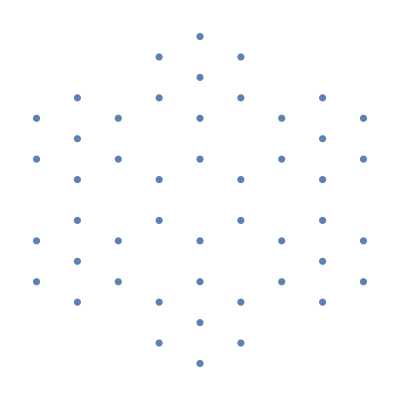

```mathematica
ListPlot[plane2D,AspectRatio->1,Axes->False]
```

```mathematica
points = Flatten[Table[{i,j,k,l},{i,1,16},{j,i+1,16},{k,j+1,16},{l,k+1,16}],3];
plane = {};
For[i=1,i≤Length[points],i++,
If[points[[i]][[1]]+points[[i]][[2]]+points[[i]][[3]]+points[[i]][[4]]==34&& Length[Union[points[[i]]]]==4,AppendTo[plane,points[[i]]]]]
Length[plane]
```

86

```mathematica
plane
```

{{1,2,15,16},{1,3,14,16},{1,4,13,16},{1,4,14,15},{1,5,12,16},{1,5,13,15},{1,6,11,16},{1,6,12,15},{1,6,13,14},{1,7,10,16},{1,7,11,15},{1,7,12,14},{1,8,9,16},{1,8,10,15},{1,8,11,14},{1,8,12,13},{1,9,10,14},{1,9,11,13},{1,10,11,12},{2,3,13,16},{2,3,14,15},{2,4,12,16},{2,4,13,15},{2,5,11,16},{2,5,12,15},{2,5,13,14},{2,6,10,16},{2,6,11,15},{2,6,12,14},{2,7,9,16},{2,7,10,15},{2,7,11,14},{2,7,12,13},{2,8,9,15},{2,8,10,14},{2,8,11,13},{2,9,10,13},{2,9,11,12},{3,4,11,16},{3,4,12,15},{3,4,13,14},{3,5,10,16},{3,5,11,15},{3,5,12,14},{3,6,9,16},{3,6,10,15},{3,6,11,14},{3,6,12,13},{3,7,8,16},{3,7,9,15},{3,7,10,14},{3,7,11,13},{3,8,9,14},{3,8,10,13},{3,8,11,12},{3,9,10,12},{4,5,9,16},{4,5,10,15},{4,5,11,14},{4,5,12,13},{4,6,8,16},{4,6,9,15},{4,6,10,14},{4,6,11,13},{4,7,8,15},{4,7,9,14},{4,7,10,13},{4,7,11,12},{4,8,9,13},{4,8,10,12},{4,9,10,11},{5,6,7,16},{5,6,8,15},{5,6,9,14},{5,6,10,13},{5,6,11,12},{5,7,8,14},{5,7,9,13},{5,7,10,12},{5,8,9,12},{5,8,10,11},{6,7,8,13},{6,7,9,12},{6,7,10,11},{6,8,9,11},{7,8,9,10}}

```mathematica
plane2 = Sort[Flatten[plane]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,13,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,14,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16,16}

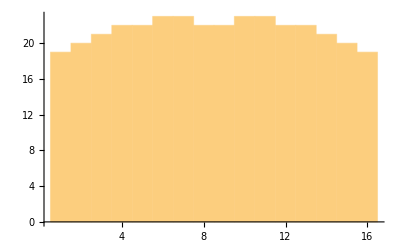

```mathematica
Histogram[plane2]
```

```mathematica
f[n_]:=Module[{points={},plane={},i},
points = Flatten[Table[{i,j,k,l},{i,1,16},{j,1,16},{k,1,16},{l,1,16}],3];
For[i=1,i≤Length[points],i++,
If[points[[i]][[1]]+points[[i]][[2]]+points[[i]][[3]]+points[[i]][[4]]==n&& Length[Union[points[[i]]]]==4,AppendTo[plane,points[[i]]]]];
Return[plane]
]
```

```mathematica
plane=f[34]
```

{{1,2,15,16},{1,2,16,15},{1,3,14,16},{1,3,16,14},{1,4,13,16},{1,4,14,15},{1,4,15,14},{1,4,16,13},{1,5,12,16},{1,5,13,15},{1,5,15,13},{1,5,16,12},2041,{16,12,2,4},{16,12,4,2},{16,12,5,1},{16,13,1,4},{16,13,2,3},{16,13,3,2},{16,13,4,1},{16,14,1,3},{16,14,3,1},{16,15,1,2},{16,15,2,1}}
 |  |  |  |

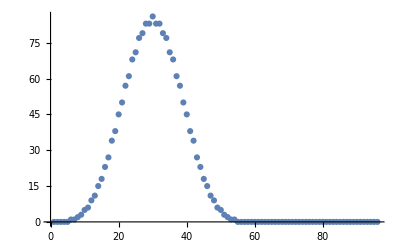

```mathematica
ListPlot[Table[Length[f[n]]/24,{n,5,100}]]
```

```mathematica
f[33]/24
```

83

Visualize all solutions by rotating them into 3D

```mathematica
normal = {1,1,1,1}
```

{1,1,1,1}

```mathematica
R = {{Cos[π/4],-Sin[π/4],0,0},{Sin[π/4],Cos[π/4],0,0},{0,0,1,0},{0,0,0,1}}
```

{{1/(√2),-1/(√2),0,0},{1/(√2),1/(√2),0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
normal2 = R.normal
```

{0,√2,1,1}

```mathematica
dot = Normalize[normal2].Normalize[{0,√2,√2,0}]
```

1/2+1/(2 √2)

```mathematica
R2 = Simplify[{{1,0,0,0},{0,1,0,0},{0,0,Cos[π/4],Sin[π/4]},{0,0,-Sin[π/4],Cos[π/4]}}];
```

```mathematica
normal3 = R2.normal2
```

{0,√2,√2,0}

```mathematica
R3 = Simplify[{{1,0,0,0},{0,Cos[π/4],Sin[π/4],0},{0,-Sin[π/4],Cos[π/4],0},{0,0,0,1}}];
```

```mathematica
R3.normal3
```

{0,2,0,0}

```mathematica
planeRotated = {};
For[i=1,i≤Length[plane],i++,
AppendTo[planeRotated,FullSimplify[R3.R2.R.(plane[[i]]-plane[[1]])]]]
```

```mathematica
plane3D = {};
For[i=1,i≤Length[planeRotated],i++,
AppendTo[plane3D,{planeRotated[[i]][[1]],planeRotated[[i]][[3]],planeRotated[[i]][[4]]}]]
```

```mathematica
ListPointPlot3D[plane3D,BoxRatios->{1,1,1}]
```

-Graphics3D-

All magic 4x4 squares

```mathematica
allFour = {{{1,2,15,16},{12,14,3,5},{13,7,10,4},{8,11,6,9}},{{1,2,15,16},{13,14,3,4},{12,7,10,5},{8,11,6,9}},{{1,2,16,15},{13,14,4,3},{12,7,9,6},{8,11,5,10}},{{1,3,14,16},{10,13,4,7},{15,6,11,2},{8,12,5,9}},{{1,3,14,16},{12,13,4,5},{15,8,9,2},{6,10,7,11}},{{1,3,14,16},{15,13,4,2},{10,6,11,7},{8,12,5,9}},{{1,3,14,16},{15,13,4,2},{12,8,9,5},{6,10,7,11}},{{1,3,16,14},{8,15,2,9},{13,6,11,4},{12,10,5,7}},{{1,3,16,14},{12,15,2,5},{13,10,7,4},{8,6,9,11}},{{1,3,16,14},{13,15,2,4},{8,6,11,9},{12,10,5,7}},{{1,3,16,14},{13,15,2,4},{12,10,7,5},{8,6,9,11}},{{1,4,13,16},{8,14,3,9},{15,5,12,2},{10,11,6,7}},{{1,4,13,16},{8,15,2,9},{14,5,12,3},{11,10,7,6}},{{1,4,13,16},{12,14,3,5},{15,9,8,2},{6,7,10,11}},{{1,4,13,16},{12,15,2,5},{14,9,8,3},{7,6,11,10}},{{1,4,13,16},{14,15,2,3},{8,5,12,9},{11,10,7,6}},{{1,4,13,16},{14,15,2,3},{12,9,8,5},{7,6,11,10}},{{1,4,13,16},{15,14,3,2},{8,5,12,9},{10,11,6,7}},{{1,4,13,16},{15,14,3,2},{12,9,8,5},{6,7,10,11}},{{1,4,14,15},{9,12,6,7},{16,5,11,2},{8,13,3,10}},{{1,4,14,15},{13,16,2,3},{8,5,11,10},{12,9,7,6}},{{1,4,14,15},{13,16,2,3},{12,9,7,6},{8,5,11,10}},{{1,4,14,15},{16,11,5,2},{9,6,12,7},{8,13,3,10}},{{1,4,14,15},{16,13,3,2},{7,6,12,9},{10,11,5,8}},{{1,4,14,15},{16,13,3,2},{11,10,8,5},{6,7,9,12}},{{1,4,15,14},{9,12,7,6},{16,5,10,3},{8,13,2,11}},{{1,4,15,14},{13,16,3,2},{8,5,10,11},{12,9,6,7}},{{1,4,15,14},{13,16,3,2},{12,9,6,7},{8,5,10,11}},{{1,4,15,14},{16,10,5,3},{9,7,12,6},{8,13,2,11}},{{1,4,15,14},{16,13,2,3},{6,7,12,9},{11,10,5,8}},{{1,4,15,14},{16,13,2,3},{10,11,8,5},{7,6,9,12}},{{1,4,16,13},{14,15,3,2},{7,6,10,11},{12,9,5,8}},{{1,4,16,13},{14,15,3,2},{11,10,6,7},{8,5,9,12}},{{1,4,16,13},{15,14,2,3},{6,7,11,10},{12,9,5,8}},{{1,4,16,13},{15,14,2,3},{10,11,7,6},{8,5,9,12}},{{1,5,12,16},{10,11,6,7},{15,4,13,2},{8,14,3,9}},{{1,5,12,16},{14,11,6,3},{15,8,9,2},{4,10,7,13}},{{1,5,12,16},{15,11,6,2},{10,4,13,7},{8,14,3,9}},{{1,5,12,16},{15,11,6,2},{14,8,9,3},{4,10,7,13}},{{1,5,16,12},{8,14,3,9},{10,4,13,7},{15,11,2,6}},{{1,5,16,12},{10,14,3,7},{8,4,13,9},{15,11,2,6}},{{1,5,16,12},{10,14,3,7},{15,11,6,2},{8,4,9,13}},{{1,5,16,12},{15,14,3,2},{10,11,6,7},{8,4,9,13}},{{1,6,11,16},{7,15,2,10},{14,4,13,3},{12,9,8,5}},{{1,6,11,16},{8,12,5,9},{15,3,14,2},{10,13,4,7}},{{1,6,11,16},{8,15,2,9},{12,3,14,5},{13,10,7,4}},{{1,6,11,16},{12,10,7,5},{13,3,14,4},{8,15,2,9}},{{1,6,11,16},{12,15,2,5},{8,3,14,9},{13,10,7,4}},{{1,6,11,16},{12,15,2,5},{14,9,8,3},{7,4,13,10}},{{1,6,11,16},{13,10,7,4},{12,3,14,5},{8,15,2,9}},{{1,6,11,16},{14,12,5,3},{15,9,8,2},{4,7,10,13}},{{1,6,11,16},{14,15,2,3},{7,4,13,10},{12,9,8,5}},{{1,6,11,16},{14,15,2,3},{12,9,8,5},{7,4,13,10}},{{1,6,11,16},{15,12,5,2},{8,3,14,9},{10,13,4,7}},{{1,6,11,16},{15,12,5,2},{14,9,8,3},{4,7,10,13}},{{1,6,12,15},{11,16,2,5},{8,3,13,10},{14,9,7,4}},{{1,6,12,15},{11,16,2,5},{14,9,7,4},{8,3,13,10}},{{1,6,12,15},{13,10,8,3},{16,7,9,2},{4,11,5,14}},{{1,6,12,15},{16,9,7,2},{13,8,10,3},{4,11,5,14}},{{1,6,12,15},{16,11,5,2},{7,4,14,9},{10,13,3,8}},{{1,6,12,15},{16,11,5,2},{13,10,8,3},{4,7,9,14}},{{1,6,15,12},{11,16,5,2},{8,3,10,13},{14,9,4,7}},{{1,6,15,12},{11,16,5,2},{14,9,4,7},{8,3,10,13}},{{1,6,15,12},{16,11,2,5},{4,7,14,9},{13,10,3,8}},{{1,6,15,12},{16,11,2,5},{10,13,8,3},{7,4,9,14}},{{1,6,16,11},{12,15,5,2},{7,4,10,13},{14,9,3,8}},{{1,6,16,11},{12,15,5,2},{13,10,4,7},{8,3,9,14}},{{1,6,16,11},{15,12,2,5},{4,7,13,10},{14,9,3,8}},{{1,6,16,11},{15,12,2,5},{10,13,7,4},{8,3,9,14}},{{1,7,10,16},{8,12,5,9},{14,2,15,3},{11,13,4,6}},{{1,7,10,16},{8,14,3,9},{12,2,15,5},{13,11,6,4}},{{1,7,10,16},{12,9,8,5},{15,4,13,2},{6,14,3,11}},{{1,7,10,16},{12,14,3,5},{8,2,15,9},{13,11,6,4}},{{1,7,10,16},{12,14,3,5},{15,9,8,2},{6,4,13,11}},{{1,7,10,16},{14,9,8,3},{15,6,11,2},{4,12,5,13}},{{1,7,10,16},{14,12,5,3},{8,2,15,9},{11,13,4,6}},{{1,7,10,16},{14,12,5,3},{15,9,8,2},{4,6,11,13}},{{1,7,10,16},{15,9,8,2},{12,4,13,5},{6,14,3,11}},{{1,7,10,16},{15,9,8,2},{14,6,11,3},{4,12,5,13}},{{1,7,10,16},{15,12,5,2},{14,9,8,3},{4,6,11,13}},{{1,7,10,16},{15,14,3,2},{12,9,8,5},{6,4,13,11}},{{1,7,12,14},{10,16,3,5},{8,2,13,11},{15,9,6,4}},{{1,7,12,14},{10,16,3,5},{15,9,6,4},{8,2,13,11}},{{1,7,12,14},{16,10,5,3},{6,4,15,9},{11,13,2,8}},{{1,7,12,14},{16,10,5,3},{13,11,8,2},{4,6,9,15}},{{1,7,14,12},{8,13,2,11},{9,4,15,6},{16,10,3,5}},{{1,7,14,12},{9,15,4,6},{8,2,13,11},{16,10,3,5}},{{1,7,14,12},{9,15,4,6},{16,10,5,3},{8,2,11,13}},{{1,7,14,12},{10,16,5,3},{8,2,11,13},{15,9,4,6}},{{1,7,14,12},{10,16,5,3},{15,9,4,6},{8,2,11,13}},{{1,7,14,12},{11,13,2,8},{6,4,15,9},{16,10,3,5}},{{1,7,14,12},{16,10,3,5},{4,6,15,9},{13,11,2,8}},{{1,7,14,12},{16,10,3,5},{11,13,8,2},{6,4,9,15}},{{1,7,16,10},{11,13,4,6},{14,12,5,3},{8,2,9,15}},{{1,7,16,10},{12,14,5,3},{6,4,11,13},{15,9,2,8}},{{1,7,16,10},{12,14,5,3},{13,11,4,6},{8,2,9,15}},{{1,7,16,10},{14,12,3,5},{4,6,13,11},{15,9,2,8}},{{1,7,16,10},{14,12,3,5},{11,13,6,4},{8,2,9,15}},{{1,7,16,10},{14,13,4,3},{11,12,5,6},{8,2,9,15}},{{1,8,9,16},{14,13,4,3},{7,2,15,10},{12,11,6,5}},{{1,8,10,15},{11,14,4,5},{16,9,7,2},{6,3,13,12}},{{1,8,10,15},{12,13,3,6},{7,2,16,9},{14,11,5,4}},{{1,8,10,15},{13,12,6,3},{16,9,7,2},{4,5,11,14}},{{1,8,10,15},{14,11,5,4},{7,2,16,9},{12,13,3,6}},{{1,8,10,15},{16,13,3,2},{5,4,14,11},{12,9,7,6}},{{1,8,11,14},{10,15,4,5},{16,9,6,3},{7,2,13,12}},{{1,8,11,14},{12,13,2,7},{6,3,16,9},{15,10,5,4}},{{1,8,11,14},{13,12,7,2},{16,9,6,3},{4,5,10,15}},{{1,8,11,14},{15,10,5,4},{6,3,16,9},{12,13,2,7}},{{1,8,12,13},{10,15,3,6},{7,2,14,11},{16,9,5,4}},{{1,8,12,13},{11,14,2,7},{6,3,15,10},{16,9,5,4}},{{1,8,12,13},{14,11,7,2},{15,10,6,3},{4,5,9,16}},{{1,8,12,13},{15,10,6,3},{14,11,7,2},{4,5,9,16}},{{1,8,13,12},{10,15,6,3},{16,9,4,5},{7,2,11,14}},{{1,8,13,12},{11,14,7,2},{16,9,4,5},{6,3,10,15}},{{1,8,13,12},{14,11,2,7},{4,5,16,9},{15,10,3,6}},{{1,8,13,12},{15,10,3,6},{4,5,16,9},{14,11,2,7}},{{1,8,13,12},{16,11,2,5},{3,6,15,10},{14,9,4,7}},{{1,8,14,11},{10,15,5,4},{7,2,12,13},{16,9,3,6}},{{1,8,14,11},{12,13,7,2},{15,10,4,5},{6,3,9,16}},{{1,8,14,11},{13,12,2,7},{4,5,15,10},{16,9,3,6}},{{1,8,14,11},{15,10,4,5},{12,13,7,2},{6,3,9,16}},{{1,8,15,10},{11,14,5,4},{6,3,12,13},{16,9,2,7}},{{1,8,15,10},{12,13,6,3},{14,11,4,5},{7,2,9,16}},{{1,8,15,10},{13,12,3,6},{4,5,14,11},{16,9,2,7}},{{1,8,15,10},{14,11,4,5},{12,13,6,3},{7,2,9,16}},{{1,9,8,16},{14,15,2,3},{7,4,13,10},{12,6,11,5}},{{1,9,16,8},{14,12,5,3},{4,6,11,13},{15,7,2,10}},{{1,9,16,8},{15,12,5,2},{4,7,10,13},{14,6,3,11}},{{1,10,7,16},{12,8,9,5},{15,3,14,2},{6,13,4,11}},{{1,10,7,16},{12,13,4,5},{15,8,9,2},{6,3,14,11}},{{1,10,7,16},{12,15,2,5},{8,3,14,9},{13,6,11,4}},{{1,10,7,16},{14,8,9,3},{15,5,12,2},{4,11,6,13}},{{1,10,7,16},{14,11,6,3},{15,8,9,2},{4,5,12,13}},{{1,10,7,16},{14,15,2,3},{8,5,12,9},{11,4,13,6}},{{1,10,7,16},{15,8,9,2},{12,3,14,5},{6,13,4,11}},{{1,10,7,16},{15,8,9,2},{14,5,12,3},{4,11,6,13}},{{1,10,7,16},{15,11,6,2},{14,8,9,3},{4,5,12,13}},{{1,10,7,16},{15,13,4,2},{12,8,9,5},{6,3,14,11}},{{1,10,8,15},{16,7,9,2},{11,4,14,5},{6,13,3,12}},{{1,10,8,15},{16,7,9,2},{13,6,12,3},{4,11,5,14}},{{1,10,8,15},{16,13,3,2},{5,4,14,11},{12,7,9,6}},{{1,10,15,8},{12,13,6,3},{5,4,11,14},{16,7,2,9}},{{1,10,15,8},{14,11,4,5},{3,6,13,12},{16,7,2,9}},{{1,10,15,8},{16,6,3,9},{5,11,14,4},{12,7,2,13}},{{1,10,15,8},{16,7,2,9},{4,11,14,5},{13,6,3,12}},{{1,10,15,8},{16,7,2,9},{6,13,12,3},{11,4,5,14}},{{1,10,16,7},{15,8,2,9},{4,11,13,6},{14,5,3,12}},{{1,10,16,7},{15,8,2,9},{6,13,11,4},{12,3,5,14}},{{1,11,6,16},{12,8,9,5},{14,2,15,3},{7,13,4,10}},{{1,11,6,16},{12,14,3,5},{8,2,15,9},{13,7,10,4}},{{1,11,6,16},{12,14,3,5},{13,7,10,4},{8,2,15,9}},{{1,11,6,16},{13,14,3,4},{12,7,10,5},{8,2,15,9}},{{1,11,6,16},{14,8,9,3},{12,2,15,5},{7,13,4,10}},{{1,11,6,16},{14,8,9,3},{15,5,12,2},{4,10,7,13}},{{1,11,6,16},{14,13,4,3},{7,2,15,10},{12,8,9,5}},{{1,11,6,16},{15,8,9,2},{14,5,12,3},{4,10,7,13}},{{1,11,6,16},{15,14,3,2},{8,5,12,9},{10,4,13,7}},{{1,11,8,14},{16,6,9,3},{10,4,15,5},{7,13,2,12}},{{1,11,8,14},{16,6,9,3},{13,7,12,2},{4,10,5,15}},{{1,11,14,8},{16,5,4,9},{7,12,13,2},{10,6,3,15}},{{1,11,14,8},{16,6,3,9},{4,10,15,5},{13,7,2,12}},{{1,11,14,8},{16,6,3,9},{7,13,12,2},{10,4,5,15}},{{1,11,16,6},{14,8,3,9},{4,10,13,7},{15,5,2,12}},{{1,11,16,6},{14,8,3,9},{7,13,10,4},{12,2,5,15}},{{1,12,5,16},{14,9,8,3},{15,6,11,2},{4,7,10,13}},{{1,12,5,16},{15,9,8,2},{14,6,11,3},{4,7,10,13}},{{1,12,5,16},{15,13,4,2},{10,6,11,7},{8,3,14,9}},{{1,12,6,15},{13,8,10,3},{16,5,11,2},{4,9,7,14}},{{1,12,6,15},{13,10,8,3},{16,7,9,2},{4,5,11,14}},{{1,12,6,15},{14,7,9,4},{11,2,16,5},{8,13,3,10}},{{1,12,6,15},{16,9,7,2},{13,8,10,3},{4,5,11,14}},{{1,12,7,14},{13,8,11,2},{16,5,10,3},{4,9,6,15}},{{1,12,7,14},{15,6,9,4},{10,3,16,5},{8,13,2,11}},{{1,12,8,13},{14,7,11,2},{15,6,10,3},{4,9,5,16}},{{1,12,8,13},{15,6,10,3},{14,7,11,2},{4,9,5,16}},{{1,12,13,8},{14,7,2,11},{4,9,16,5},{15,6,3,10}},{{1,12,13,8},{15,6,3,10},{4,9,16,5},{14,7,2,11}},{{1,12,13,8},{15,10,3,6},{2,7,14,11},{16,5,4,9}},{{1,12,13,8},{16,7,2,9},{3,10,15,6},{14,5,4,11}},{{1,12,13,8},{16,9,4,5},{2,7,14,11},{15,6,3,10}},{{1,12,14,7},{13,8,2,11},{4,9,15,6},{16,5,3,10}},{{1,12,14,7},{15,6,4,9},{8,13,11,2},{10,3,5,16}},{{1,12,15,6},{13,8,3,10},{4,9,14,7},{16,5,2,11}},{{1,12,15,6},{14,7,4,9},{8,13,10,3},{11,2,5,16}},{{1,12,15,6},{14,9,4,7},{3,8,13,10},{16,5,2,11}},{{1,13,4,16},{14,8,9,3},{12,2,15,5},{7,11,6,10}},{{1,13,4,16},{14,12,5,3},{8,2,15,9},{11,7,10,6}},{{1,13,4,16},{15,8,9,2},{12,3,14,5},{6,10,7,11}},{{1,13,4,16},{15,12,5,2},{8,3,14,9},{10,6,11,7}},{{1,13,8,12},{16,4,9,5},{10,6,15,3},{7,11,2,14}},{{1,13,8,12},{16,4,9,5},{11,7,14,2},{6,10,3,15}},{{1,13,8,12},{16,11,2,5},{3,6,15,10},{14,4,9,7}},{{1,13,12,8},{15,10,3,6},{2,7,14,11},{16,4,5,9}},{{1,13,12,8},{16,4,5,9},{6,10,15,3},{11,7,2,14}},{{1,13,12,8},{16,4,5,9},{7,11,14,2},{10,6,3,15}},{{1,13,12,8},{16,7,2,9},{3,10,15,6},{14,4,5,11}},{{1,14,3,16},{15,9,8,2},{12,4,13,5},{6,7,10,11}},{{1,14,3,16},{15,11,6,2},{10,4,13,7},{8,5,12,9}},{{1,14,4,15},{16,11,5,2},{9,6,12,7},{8,3,13,10}},{{1,14,7,12},{15,4,9,6},{10,5,16,3},{8,11,2,13}},{{1,14,7,12},{16,5,10,3},{9,4,15,6},{8,11,2,13}},{{1,14,8,11},{15,4,10,5},{12,7,13,2},{6,9,3,16}},{{1,14,11,8},{15,4,5,10},{6,9,16,3},{12,7,2,13}},{{1,14,11,8},{16,5,4,9},{7,12,13,2},{10,3,6,15}},{{1,14,12,7},{15,4,6,9},{8,11,13,2},{10,5,3,16}},{{1,15,4,14},{16,10,5,3},{9,7,12,6},{8,2,13,11}},{{1,15,10,8},{16,6,3,9},{5,11,14,4},{12,2,7,13}},{{2,1,15,16},{14,13,3,4},{11,8,10,5},{7,12,6,9}},{{2,1,16,15},{11,13,4,6},{14,8,9,3},{7,12,5,10}},{{2,1,16,15},{14,13,4,3},{11,8,9,6},{7,12,5,10}},{{2,3,13,16},{10,11,5,8},{15,6,12,1},{7,14,4,9}},{{2,3,13,16},{14,15,1,4},{7,6,12,9},{11,10,8,5}},{{2,3,13,16},{14,15,1,4},{11,10,8,5},{7,6,12,9}},{{2,3,13,16},{15,12,6,1},{10,5,11,8},{7,14,4,9}},{{2,3,13,16},{15,14,4,1},{8,5,11,10},{9,12,6,7}},{{2,3,13,16},{15,14,4,1},{12,9,7,6},{5,8,10,11}},{{2,3,14,15},{7,13,4,10},{16,6,11,1},{9,12,5,8}},{{2,3,14,15},{7,16,1,10},{13,6,11,4},{12,9,8,5}},{{2,3,14,15},{8,16,1,9},{11,5,12,6},{13,10,7,4}},{{2,3,14,15},{11,13,4,6},{16,10,7,1},{5,8,9,12}},{{2,3,14,15},{11,16,1,6},{8,5,12,9},{13,10,7,4}},{{2,3,14,15},{11,16,1,6},{13,10,7,4},{8,5,12,9}},{{2,3,14,15},{13,16,1,4},{7,6,11,10},{12,9,8,5}},{{2,3,14,15},{13,16,1,4},{11,10,7,6},{8,5,12,9}},{{2,3,14,15},{16,13,4,1},{7,6,11,10},{9,12,5,8}},{{2,3,14,15},{16,13,4,1},{11,10,7,6},{5,8,9,12}},{{2,3,15,14},{13,16,4,1},{8,5,9,12},{11,10,6,7}},{{2,3,15,14},{13,16,4,1},{12,9,5,8},{7,6,10,11}},{{2,3,15,14},{16,13,1,4},{5,8,12,9},{11,10,6,7}},{{2,3,15,14},{16,13,1,4},{9,12,8,5},{7,6,10,11}},{{2,3,16,13},{10,11,8,5},{15,6,9,4},{7,14,1,12}},{{2,3,16,13},{14,15,4,1},{7,6,9,12},{11,10,5,8}},{{2,3,16,13},{14,15,4,1},{11,10,5,8},{7,6,9,12}},{{2,3,16,13},{15,9,6,4},{10,8,11,5},{7,14,1,12}},{{2,3,16,13},{15,14,1,4},{5,8,11,10},{12,9,6,7}},{{2,3,16,13},{15,14,1,4},{9,12,7,6},{8,5,10,11}},{{2,4,13,15},{14,16,3,1},{7,5,10,12},{11,9,8,6}},{{2,4,13,15},{14,16,3,1},{11,9,6,8},{7,5,12,10}},{{2,4,13,15},{16,14,1,3},{5,7,12,10},{11,9,8,6}},{{2,4,13,15},{16,14,1,3},{9,11,8,6},{7,5,12,10}},{{2,4,15,13},{5,14,3,12},{16,7,10,1},{11,9,6,8}},{{2,4,15,13},{9,14,3,8},{16,11,6,1},{7,5,10,12}},{{2,4,15,13},{16,14,3,1},{5,7,10,12},{11,9,6,8}},{{2,4,15,13},{16,14,3,1},{9,11,6,8},{7,5,10,12}},{{2,5,11,16},{12,15,1,6},{7,4,14,9},{13,10,8,3}},{{2,5,11,16},{12,15,1,6},{13,10,8,3},{7,4,14,9}},{{2,5,11,16},{14,9,7,4},{15,8,10,1},{3,12,6,13}},{{2,5,11,16},{15,10,8,1},{14,7,9,4},{3,12,6,13}},{{2,5,11,16},{15,12,6,1},{8,3,13,10},{9,14,4,7}},{{2,5,11,16},{15,12,6,1},{14,9,7,4},{3,8,10,13}},{{2,5,12,15},{7,11,6,10},{16,4,13,1},{9,14,3,8}},{{2,5,12,15},{7,16,1,10},{11,4,13,6},{14,9,8,3}},{{2,5,12,15},{11,9,8,6},{14,4,13,3},{7,16,1,10}},{{2,5,12,15},{11,16,1,6},{7,4,13,10},{14,9,8,3}},{{2,5,12,15},{11,16,1,6},{13,10,7,4},{8,3,14,9}},{{2,5,12,15},{13,11,6,4},{16,10,7,1},{3,8,9,14}},{{2,5,12,15},{13,16,1,4},{11,10,7,6},{8,3,14,9}},{{2,5,12,15},{14,9,8,3},{11,4,13,6},{7,16,1,10}},{{2,5,12,15},{14,16,3,1},{11,9,6,8},{7,4,13,10}},{{2,5,12,15},{16,11,6,1},{7,4,13,10},{9,14,3,8}},{{2,5,12,15},{16,11,6,1},{13,10,7,4},{3,8,9,14}},{{2,5,12,15},{16,14,1,3},{9,11,8,6},{7,4,13,10}},{{2,5,15,12},{11,16,6,1},{8,3,9,14},{13,10,4,7}},{{2,5,15,12},{11,16,6,1},{14,9,3,8},{7,4,10,13}},{{2,5,15,12},{16,11,1,6},{3,8,14,9},{13,10,4,7}},{{2,5,15,12},{16,11,1,6},{9,14,8,3},{7,4,10,13}},{{2,5,16,11},{8,12,1,13},{9,7,14,4},{15,10,3,6}},{{2,5,16,11},{12,15,6,1},{7,4,9,14},{13,10,3,8}},{{2,5,16,11},{12,15,6,1},{13,10,3,8},{7,4,9,14}},{{2,5,16,11},{13,12,1,8},{4,7,14,9},{15,10,3,6}},{{2,5,16,11},{15,10,3,6},{4,7,14,9},{13,12,1,8}},{{2,5,16,11},{15,12,1,6},{3,8,13,10},{14,9,4,7}},{{2,5,16,11},{15,12,1,6},{9,14,7,4},{8,3,10,13}},{{2,6,15,11},{7,13,4,10},{9,3,14,8},{16,12,1,5}},{{2,6,15,11},{9,13,4,8},{7,3,14,10},{16,12,1,5}},{{2,6,15,11},{9,13,4,8},{16,12,5,1},{7,3,10,14}},{{2,6,15,11},{16,13,4,1},{9,12,5,8},{7,3,10,14}},{{2,7,9,16},{11,14,4,5},{8,1,15,10},{13,12,6,3}},{{2,7,9,16},{12,13,3,6},{15,10,8,1},{5,4,14,11}},{{2,7,9,16},{13,12,6,3},{8,1,15,10},{11,14,4,5}},{{2,7,9,16},{14,11,5,4},{15,10,8,1},{3,6,12,13}},{{2,7,9,16},{15,14,4,1},{6,3,13,12},{11,10,8,5}},{{2,7,10,15},{8,12,5,9},{11,1,16,6},{13,14,3,4}},{{2,7,10,15},{11,12,5,6},{8,1,16,9},{13,14,3,4}},{{2,7,11,14},{8,13,1,12},{9,4,16,5},{15,10,6,3}},{{2,7,11,14},{9,16,4,5},{8,1,13,12},{15,10,6,3}},{{2,7,11,14},{12,13,1,8},{5,4,16,9},{15,10,6,3}},{{2,7,11,14},{13,12,8,1},{16,9,5,4},{3,6,10,15}},{{2,7,11,14},{16,9,5,4},{13,12,8,1},{3,6,10,15}},{{2,7,12,13},{9,16,3,6},{15,10,5,4},{8,1,14,11}},{{2,7,12,13},{11,14,1,8},{5,4,15,10},{16,9,6,3}},{{2,7,12,13},{14,11,8,1},{15,10,5,4},{3,6,9,16}},{{2,7,12,13},{16,9,6,3},{5,4,15,10},{11,14,1,8}},{{2,7,13,12},{8,11,1,14},{9,6,16,3},{15,10,4,5}},{{2,7,13,12},{9,16,6,3},{8,1,11,14},{15,10,4,5}},{{2,7,13,12},{11,14,8,1},{16,9,3,6},{5,4,10,15}},{{2,7,13,12},{14,11,1,8},{3,6,16,9},{15,10,4,5}},{{2,7,13,12},{16,9,3,6},{11,14,8,1},{5,4,10,15}},{{2,7,14,11},{8,10,3,13},{9,5,16,4},{15,12,1,6}},{{2,7,14,11},{9,16,5,4},{15,10,3,6},{8,1,12,13}},{{2,7,14,11},{12,13,8,1},{15,10,3,6},{5,4,9,16}},{{2,7,14,11},{13,10,3,8},{4,5,16,9},{15,12,1,6}},{{2,7,14,11},{13,12,1,8},{3,6,15,10},{16,9,4,5}},{{2,7,14,11},{16,9,4,5},{3,6,15,10},{13,12,1,8}},{{2,7,16,9},{11,14,5,4},{13,12,3,6},{8,1,10,15}},{{2,7,16,9},{12,13,6,3},{5,4,11,14},{15,10,1,8}},{{2,7,16,9},{13,12,3,6},{11,14,5,4},{8,1,10,15}},{{2,7,16,9},{14,11,4,5},{3,6,13,12},{15,10,1,8}},{{2,8,9,15},{11,13,4,6},{7,1,16,10},{14,12,5,3}},{{2,8,9,15},{11,13,4,6},{16,10,7,1},{5,3,14,12}},{{2,8,9,15},{13,11,6,4},{7,1,16,10},{12,14,3,5}},{{2,8,9,15},{13,11,6,4},{16,10,7,1},{3,5,12,14}},{{2,8,9,15},{16,11,6,1},{13,10,7,4},{3,5,12,14}},{{2,8,9,15},{16,13,4,1},{11,10,7,6},{5,3,14,12}},{{2,8,11,13},{9,15,4,6},{7,1,14,12},{16,10,5,3}},{{2,8,11,13},{9,15,4,6},{16,10,5,3},{7,1,14,12}},{{2,8,11,13},{10,16,5,3},{7,1,12,14},{15,9,6,4}},{{2,8,11,13},{10,16,5,3},{15,9,4,6},{7,1,14,12}},{{2,8,11,13},{14,12,1,7},{3,5,16,10},{15,9,6,4}},{{2,8,11,13},{15,9,6,4},{5,3,16,10},{12,14,1,7}},{{2,8,11,13},{15,9,6,4},{14,12,7,1},{3,5,10,16}},{{2,8,13,11},{9,15,6,4},{7,1,12,14},{16,10,3,5}},{{2,8,13,11},{9,15,6,4},{16,10,3,5},{7,1,12,14}},{{2,8,13,11},{15,9,4,6},{3,5,16,10},{14,12,1,7}},{{2,8,13,11},{15,9,4,6},{12,14,7,1},{5,3,10,16}},{{2,8,15,9},{11,12,5,6},{14,13,4,3},{7,1,10,16}},{{2,8,15,9},{11,13,6,4},{5,3,12,14},{16,10,1,7}},{{2,8,15,9},{11,13,6,4},{14,12,3,5},{7,1,10,16}},{{2,8,15,9},{13,11,4,6},{3,5,14,12},{16,10,1,7}},{{2,8,15,9},{13,11,4,6},{12,14,5,3},{7,1,10,16}},{{2,8,15,9},{14,12,5,3},{11,13,4,6},{7,1,10,16}},{{2,9,7,16},{15,8,10,1},{12,3,13,6},{5,14,4,11}},{{2,9,7,16},{15,8,10,1},{14,5,11,4},{3,12,6,13}},{{2,9,7,16},{15,14,4,1},{6,3,13,12},{11,8,10,5}},{{2,9,8,15},{11,7,10,6},{16,4,13,1},{5,14,3,12}},{{2,9,8,15},{11,16,1,6},{7,4,13,10},{14,5,12,3}},{{2,9,8,15},{13,7,10,4},{16,6,11,1},{3,12,5,14}},{{2,9,8,15},{13,16,1,4},{7,6,11,10},{12,3,14,5}},{{2,9,8,15},{14,16,3,1},{7,5,10,12},{11,4,13,6}},{{2,9,8,15},{16,7,10,1},{11,4,13,6},{5,14,3,12}},{{2,9,8,15},{16,7,10,1},{13,6,11,4},{3,12,5,14}},{{2,9,8,15},{16,14,1,3},{5,7,12,10},{11,4,13,6}},{{2,9,15,8},{16,7,1,10},{3,12,14,5},{13,6,4,11}},{{2,9,15,8},{16,7,1,10},{5,14,12,3},{11,4,6,13}},{{2,9,16,7},{12,8,1,13},{5,11,14,4},{15,6,3,10}},{{2,9,16,7},{13,8,1,12},{4,11,14,5},{15,6,3,10}},{{2,9,16,7},{15,5,4,10},{6,12,13,3},{11,8,1,14}},{{2,9,16,7},{15,6,3,10},{4,11,14,5},{13,8,1,12}},{{2,9,16,7},{15,8,1,10},{3,12,13,6},{14,5,4,11}},{{2,9,16,7},{15,8,1,10},{5,14,11,4},{12,3,6,13}},{{2,10,7,15},{11,16,1,6},{8,5,12,9},{13,3,14,4}},{{2,10,15,7},{13,11,6,4},{3,5,12,14},{16,8,1,9}},{{2,10,15,7},{16,11,6,1},{3,8,9,14},{13,5,4,12}},{{2,11,5,16},{13,8,10,3},{12,1,15,6},{7,14,4,9}},{{2,11,5,16},{14,7,9,4},{15,6,12,1},{3,10,8,13}},{{2,11,5,16},{14,9,7,4},{15,8,10,1},{3,6,12,13}},{{2,11,5,16},{15,10,8,1},{14,7,9,4},{3,6,12,13}},{{2,11,7,14},{12,13,1,8},{5,4,16,9},{15,6,10,3}},{{2,11,7,14},{13,8,12,1},{16,5,9,4},{3,10,6,15}},{{2,11,7,14},{16,5,9,4},{13,8,12,1},{3,10,6,15}},{{2,11,8,13},{14,7,12,1},{15,6,9,4},{3,10,5,16}},{{2,11,8,13},{14,12,1,7},{3,5,16,10},{15,6,9,4}},{{2,11,8,13},{15,4,9,6},{10,5,16,3},{7,14,1,12}},{{2,11,8,13},{16,5,10,3},{9,4,15,6},{7,14,1,12}},{{2,11,13,8},{12,7,1,14},{5,10,16,3},{15,6,4,9}},{{2,11,13,8},{14,7,1,12},{3,10,16,5},{15,6,4,9}},{{2,11,13,8},{16,5,3,10},{7,14,12,1},{9,4,6,15}},{{2,11,14,7},{12,6,3,13},{5,9,16,4},{15,8,1,10}},{{2,11,14,7},{12,13,8,1},{5,4,9,16},{15,6,3,10}},{{2,11,14,7},{13,6,3,12},{4,9,16,5},{15,8,1,10}},{{2,11,14,7},{13,8,1,12},{3,10,15,6},{16,5,4,9}},{{2,11,14,7},{15,4,5,10},{8,13,12,1},{9,6,3,16}},{{2,11,14,7},{15,10,3,6},{1,8,13,12},{16,5,4,9}},{{2,11,14,7},{16,5,4,9},{3,10,15,6},{13,8,1,12}},{{2,11,14,7},{16,9,4,5},{1,8,13,12},{15,6,3,10}},{{2,11,16,5},{13,8,3,10},{7,14,9,4},{12,1,6,15}},{{2,11,16,5},{14,7,4,9},{3,10,13,8},{15,6,1,12}},{{2,12,5,15},{13,7,10,4},{11,1,16,6},{8,14,3,9}},{{2,12,5,15},{13,7,10,4},{16,6,11,1},{3,9,8,14}},{{2,12,5,15},{14,13,4,3},{11,8,9,6},{7,1,16,10}},{{2,12,5,15},{16,7,10,1},{13,6,11,4},{3,9,8,14}},{{2,12,5,15},{16,13,4,1},{7,6,11,10},{9,3,14,8}},{{2,12,7,13},{15,5,10,4},{9,3,16,6},{8,14,1,11}},{{2,12,7,13},{15,5,10,4},{14,8,11,1},{3,9,6,16}},{{2,12,13,7},{15,5,4,10},{3,9,16,6},{14,8,1,11}},{{2,12,13,7},{15,5,4,10},{8,14,11,1},{9,3,6,16}},{{2,12,15,5},{13,7,4,10},{3,9,14,8},{16,6,1,11}},{{2,12,15,5},{13,7,4,10},{8,14,9,3},{11,1,6,16}},{{2,13,3,16},{15,12,6,1},{10,5,11,8},{7,4,14,9}},{{2,13,7,12},{14,11,1,8},{3,6,16,9},{15,4,10,5}},{{2,13,7,12},{16,3,9,6},{11,8,14,1},{5,10,4,15}},{{2,13,8,11},{16,3,10,5},{9,6,15,4},{7,12,1,14}},{{2,13,11,8},{14,7,1,12},{3,10,16,5},{15,4,6,9}},{{2,13,11,8},{16,3,5,10},{7,12,14,1},{9,6,4,15}},{{2,13,12,7},{16,3,6,9},{5,10,15,4},{11,8,1,14}},{{2,14,3,15},{16,7,10,1},{11,4,13,6},{5,9,8,12}},{{2,14,3,15},{16,11,6,1},{7,4,13,10},{9,5,12,8}},{{2,14,7,11},{15,3,10,6},{9,5,16,4},{8,12,1,13}},{{2,14,7,11},{15,3,10,6},{12,8,13,1},{5,9,4,16}},{{2,14,11,7},{15,3,6,10},{5,9,16,4},{12,8,1,13}},{{2,14,11,7},{15,3,6,10},{8,12,13,1},{9,5,4,16}},{{2,14,11,7},{15,4,5,10},{8,13,12,1},{9,3,6,16}},{{2,14,11,7},{16,9,4,5},{1,8,13,12},{15,3,6,10}},{{2,15,4,13},{16,6,11,1},{9,3,14,8},{7,10,5,12}},{{2,15,4,13},{16,10,7,1},{5,3,14,12},{11,6,9,8}},{{2,15,6,11},{16,5,12,1},{9,4,13,8},{7,10,3,14}},{{2,15,10,7},{16,9,8,1},{3,6,11,14},{13,4,5,12}},{{3,1,14,16},{8,15,2,9},{13,6,11,4},{10,12,7,5}},{{3,1,14,16},{12,15,2,5},{13,10,7,4},{6,8,11,9}},{{3,1,14,16},{13,15,2,4},{8,6,11,9},{10,12,7,5}},{{3,1,14,16},{13,15,2,4},{12,10,7,5},{6,8,11,9}},{{3,1,16,14},{13,15,4,2},{8,6,9,11},{10,12,5,7}},{{3,1,16,14},{13,15,4,2},{12,10,5,7},{6,8,9,11}},{{3,1,16,14},{15,13,2,4},{6,8,11,9},{10,12,5,7}},{{3,1,16,14},{15,13,2,4},{10,12,7,5},{6,8,9,11}},{{3,2,13,16},{11,10,5,8},{14,7,12,1},{6,15,4,9}},{{3,2,13,16},{14,12,7,1},{11,5,10,8},{6,15,4,9}},{{3,2,13,16},{14,15,4,1},{8,5,10,11},{9,12,7,6}},{{3,2,13,16},{14,15,4,1},{12,9,6,7},{5,8,11,10}},{{3,2,13,16},{15,14,1,4},{6,7,12,9},{10,11,8,5}},{{3,2,13,16},{15,14,1,4},{10,11,8,5},{6,7,12,9}},{{3,2,14,15},{13,16,4,1},{8,5,9,12},{10,11,7,6}},{{3,2,14,15},{13,16,4,1},{12,9,5,8},{6,7,11,10}},{{3,2,14,15},{16,13,1,4},{5,8,12,9},{10,11,7,6}},{{3,2,14,15},{16,13,1,4},{9,12,8,5},{6,7,11,10}},{{3,2,15,14},{6,13,4,11},{16,7,10,1},{9,12,5,8}},{{3,2,15,14},{6,16,1,11},{13,7,10,4},{12,9,8,5}},{{3,2,15,14},{10,13,4,7},{16,11,6,1},{5,8,9,12}},{{3,2,15,14},{10,16,1,7},{13,11,6,4},{8,5,12,9}},{{3,2,15,14},{12,16,5,1},{13,9,4,8},{6,7,10,11}},{{3,2,15,14},{13,16,1,4},{6,7,10,11},{12,9,8,5}},{{3,2,15,14},{13,16,1,4},{10,11,6,7},{8,5,12,9}},{{3,2,15,14},{16,12,1,5},{9,13,8,4},{6,7,10,11}},{{3,2,15,14},{16,13,4,1},{6,7,10,11},{9,12,5,8}},{{3,2,15,14},{16,13,4,1},{10,11,6,7},{5,8,9,12}},{{3,2,16,13},{7,12,6,9},{14,5,11,4},{10,15,1,8}},{{3,2,16,13},{8,15,1,10},{9,6,12,7},{14,11,5,4}},{{3,2,16,13},{10,15,1,8},{7,6,12,9},{14,11,5,4}},{{3,2,16,13},{11,10,8,5},{14,7,9,4},{6,15,1,12}},{{3,2,16,13},{14,9,7,4},{11,8,10,5},{6,15,1,12}},{{3,2,16,13},{14,11,5,4},{7,6,12,9},{10,15,1,8}},{{3,2,16,13},{14,15,1,4},{5,8,10,11},{12,9,7,6}},{{3,2,16,13},{14,15,1,4},{9,12,6,7},{8,5,11,10}},{{3,2,16,13},{15,14,4,1},{6,7,9,12},{10,11,5,8}},{{3,2,16,13},{15,14,4,1},{10,11,5,8},{6,7,9,12}},{{3,4,13,14},{6,16,1,11},{15,9,8,2},{10,5,12,7}},{{3,4,13,14},{15,16,1,2},{6,9,8,11},{10,5,12,7}},{{3,4,14,13},{15,16,2,1},{6,9,7,12},{10,5,11,8}},{{3,5,10,16},{12,14,1,7},{13,11,8,2},{6,4,15,9}},{{3,5,10,16},{14,12,7,1},{8,2,13,11},{9,15,4,6}},{{3,5,12,14},{6,10,7,11},{16,4,13,1},{9,15,2,8}},{{3,5,12,14},{6,11,8,9},{15,2,13,4},{10,16,1,7}},{{3,5,12,14},{6,16,1,11},{15,9,8,2},{10,4,13,7}},{{3,5,12,14},{8,9,6,11},{13,4,15,2},{10,16,1,7}},{{3,5,12,14},{10,16,1,7},{13,11,6,4},{8,2,15,9}},{{3,5,12,14},{13,16,1,4},{10,11,6,7},{8,2,15,9}},{{3,5,12,14},{15,16,1,2},{6,9,8,11},{10,4,13,7}},{{3,5,12,14},{16,10,7,1},{6,4,13,11},{9,15,2,8}},{{3,5,14,12},{10,16,7,1},{8,2,9,15},{13,11,4,6}},{{3,5,14,12},{10,16,7,1},{15,9,2,8},{6,4,11,13}},{{3,5,14,12},{16,10,1,7},{2,8,15,9},{13,11,4,6}},{{3,5,14,12},{16,10,1,7},{9,15,8,2},{6,4,11,13}},{{3,5,16,10},{12,14,7,1},{6,4,9,15},{13,11,2,8}},{{3,5,16,10},{12,14,7,1},{13,11,2,8},{6,4,9,15}},{{3,5,16,10},{14,12,1,7},{2,8,13,11},{15,9,4,6}},{{3,5,16,10},{14,12,1,7},{9,15,6,4},{8,2,11,13}},{{3,6,9,16},{12,13,2,7},{14,11,8,1},{5,4,15,10}},{{3,6,9,16},{13,12,7,2},{8,1,14,11},{10,15,4,5}},{{3,6,12,13},{8,11,5,10},{9,2,16,7},{14,15,1,4}},{{3,6,12,13},{9,16,2,7},{14,11,5,4},{8,1,15,10}},{{3,6,12,13},{10,11,5,8},{7,2,16,9},{14,15,1,4}},{{3,6,12,13},{16,9,7,2},{5,4,14,11},{10,15,1,8}},{{3,6,13,12},{8,10,1,15},{9,7,16,2},{14,11,4,5}},{{3,6,13,12},{9,16,7,2},{8,1,10,15},{14,11,4,5}},{{3,6,13,12},{10,15,8,1},{16,9,2,7},{5,4,11,14}},{{3,6,13,12},{15,10,1,8},{2,7,16,9},{14,11,4,5}},{{3,6,13,12},{16,9,2,7},{10,15,8,1},{5,4,11,14}},{{3,6,15,10},{9,16,5,4},{14,11,2,7},{8,1,12,13}},{{3,6,15,10},{12,8,1,13},{5,9,16,4},{14,11,2,7}},{{3,6,15,10},{12,13,8,1},{14,11,2,7},{5,4,9,16}},{{3,6,15,10},{13,8,1,12},{4,9,16,5},{14,11,2,7}},{{3,6,15,10},{13,12,1,8},{2,7,14,11},{16,9,4,5}},{{3,6,15,10},{14,7,2,11},{4,9,16,5},{13,12,1,8}},{{3,6,15,10},{16,9,4,5},{2,7,14,11},{13,12,1,8}},{{3,6,15,10},{16,11,2,5},{1,8,13,12},{14,9,4,7}},{{3,6,16,9},{10,15,5,4},{13,12,2,7},{8,1,11,14}},{{3,6,16,9},{12,13,7,2},{5,4,10,15},{14,11,1,8}},{{3,6,16,9},{13,12,2,7},{10,15,5,4},{8,1,11,14}},{{3,6,16,9},{15,10,4,5},{2,7,13,12},{14,11,1,8}},{{3,7,10,14},{12,16,5,1},{6,2,11,15},{13,9,8,4}},{{3,7,10,14},{12,16,5,1},{13,9,4,8},{6,2,15,11}},{{3,7,10,14},{16,12,1,5},{2,6,15,11},{13,9,8,4}},{{3,7,10,14},{16,12,1,5},{9,13,8,4},{6,2,15,11}},{{3,7,14,10},{9,12,5,8},{16,13,4,1},{6,2,11,15}},{{3,7,14,10},{16,12,5,1},{2,6,11,15},{13,9,4,8}},{{3,7,14,10},{16,12,5,1},{9,13,4,8},{6,2,11,15}},{{3,8,9,14},{10,13,4,7},{16,11,6,1},{5,2,15,12}},{{3,8,9,14},{13,10,7,4},{6,1,16,11},{12,15,2,5}},{{3,8,9,14},{13,15,4,2},{12,10,5,7},{6,1,16,11}},{{3,8,9,14},{15,13,2,4},{10,12,7,5},{6,1,16,11}},{{3,8,9,14},{16,13,4,1},{10,11,6,7},{5,2,15,12}},{{3,8,10,13},{9,14,4,7},{16,11,5,2},{6,1,15,12}},{{3,8,10,13},{14,9,7,4},{5,2,16,11},{12,15,1,6}},{{3,8,13,10},{9,14,7,4},{6,1,12,15},{16,11,2,5}},{{3,8,13,10},{9,14,7,4},{16,11,2,5},{6,1,12,15}},{{3,8,13,10},{14,9,4,7},{2,5,16,11},{15,12,1,6}},{{3,8,13,10},{14,9,4,7},{12,15,6,1},{5,2,11,16}},{{3,8,13,10},{14,11,2,7},{1,6,15,12},{16,9,4,5}},{{3,8,13,10},{16,9,4,5},{1,6,15,12},{14,11,2,7}},{{3,8,14,9},{10,13,7,4},{5,2,12,15},{16,11,1,6}},{{3,8,14,9},{10,13,7,4},{15,12,2,5},{6,1,11,16}},{{3,8,14,9},{13,10,4,7},{2,5,15,12},{16,11,1,6}},{{3,8,14,9},{13,10,4,7},{12,15,5,2},{6,1,11,16}},{{3,9,6,16},{14,8,11,1},{12,2,13,7},{5,15,4,10}},{{3,9,8,14},{10,6,11,7},{16,4,13,1},{5,15,2,12}},{{3,9,8,14},{10,7,12,5},{15,2,13,4},{6,16,1,11}},{{3,9,8,14},{12,5,10,7},{13,4,15,2},{6,16,1,11}},{{3,9,8,14},{12,16,5,1},{6,2,11,15},{13,7,10,4}},{{3,9,8,14},{13,16,1,4},{6,7,10,11},{12,2,15,5}},{{3,9,8,14},{16,6,11,1},{10,4,13,7},{5,15,2,12}},{{3,9,8,14},{16,12,1,5},{2,6,15,11},{13,7,10,4}},{{3,9,14,8},{16,6,1,11},{2,12,15,5},{13,7,4,10}},{{3,9,14,8},{16,6,1,11},{5,15,12,2},{10,4,7,13}},{{3,9,16,6},{10,8,1,15},{7,13,12,2},{14,4,5,11}},{{3,9,16,6},{14,4,5,11},{7,13,12,2},{10,8,1,15}},{{3,9,16,6},{14,8,1,11},{2,12,13,7},{15,5,4,10}},{{3,9,16,6},{14,8,1,11},{5,15,10,4},{12,2,7,13}},{{3,9,16,6},{15,8,1,10},{2,13,12,7},{14,4,5,11}},{{3,10,5,16},{13,8,11,2},{12,1,14,7},{6,15,4,9}},{{3,10,7,14},{13,4,9,8},{12,5,16,1},{6,15,2,11}},{{3,10,8,13},{16,5,11,2},{9,4,14,7},{6,15,1,12}},{{3,10,13,8},{12,6,1,15},{5,11,16,2},{14,7,4,9}},{{3,10,13,8},{15,6,1,12},{2,11,16,5},{14,7,4,9}},{{3,10,13,8},{16,5,2,11},{6,15,12,1},{9,4,7,14}},{{3,10,15,6},{13,8,1,12},{2,11,14,7},{16,5,4,9}},{{3,10,15,6},{16,5,4,9},{2,11,14,7},{13,8,1,12}},{{3,10,15,6},{16,7,2,9},{1,12,13,8},{14,5,4,11}},{{3,10,16,5},{13,8,2,11},{6,15,9,4},{12,1,7,14}},{{3,10,16,5},{15,6,4,9},{2,11,13,8},{14,7,1,12}},{{3,11,14,6},{13,10,7,4},{2,5,12,15},{16,8,1,9}},{{3,11,14,6},{16,10,7,1},{2,8,9,15},{13,5,4,12}},{{3,12,5,14},{13,6,11,4},{10,1,16,7},{8,15,2,9}},{{3,12,5,14},{13,15,4,2},{8,6,9,11},{10,1,16,7}},{{3,12,5,14},{15,8,9,2},{6,1,16,11},{10,13,4,7}},{{3,12,5,14},{15,13,2,4},{6,8,11,9},{10,1,16,7}},{{3,12,5,14},{16,13,4,1},{6,7,10,11},{9,2,15,8}},{{3,12,6,13},{14,5,11,4},{9,2,16,7},{8,15,1,10}},{{3,12,13,6},{14,5,4,11},{2,9,16,7},{15,8,1,10}},{{3,12,13,6},{14,5,4,11},{8,15,10,1},{9,2,7,16}},{{3,12,13,6},{14,7,2,11},{1,10,15,8},{16,5,4,9}},{{3,12,13,6},{16,5,4,9},{1,10,15,8},{14,7,2,11}},{{3,12,14,5},{13,6,4,11},{2,9,15,8},{16,7,1,10}},{{3,12,14,5},{13,6,4,11},{8,15,9,2},{10,1,7,16}},{{3,13,2,16},{14,12,7,1},{11,5,10,8},{6,4,15,9}},{{3,13,4,14},{15,8,9,2},{6,1,16,11},{10,12,5,7}},{{3,13,6,12},{15,10,1,8},{2,7,16,9},{14,4,11,5}},{{3,13,6,12},{16,2,9,7},{10,8,15,1},{5,11,4,14}},{{3,13,8,10},{14,11,2,7},{1,6,15,12},{16,4,9,5}},{{3,13,8,10},{16,2,11,5},{9,7,14,4},{6,12,1,15}},{{3,13,10,8},{15,6,1,12},{2,11,16,5},{14,4,7,9}},{{3,13,10,8},{16,2,5,11},{6,12,15,1},{9,7,4,14}},{{3,13,12,6},{14,7,2,11},{1,10,15,8},{16,4,5,9}},{{3,13,12,6},{15,4,5,10},{2,9,16,7},{14,8,1,11}},{{3,13,12,6},{16,2,7,9},{5,11,14,4},{10,8,1,15}},{{3,14,5,12},{15,2,9,8},{10,7,16,1},{6,11,4,13}},{{3,14,7,10},{16,4,13,1},{9,5,12,8},{6,11,2,15}},{{3,14,7,10},{16,11,6,1},{2,5,12,15},{13,4,9,8}},{{3,14,8,9},{15,2,12,5},{10,7,13,4},{6,11,1,16}},{{3,14,9,8},{15,2,5,12},{6,11,16,1},{10,7,4,13}},{{3,14,11,6},{16,9,8,1},{2,7,10,15},{13,4,5,12}},{{3,14,12,5},{15,2,8,9},{6,11,13,4},{10,7,1,16}},{{3,15,2,14},{16,6,11,1},{10,4,13,7},{5,9,8,12}},{{3,15,2,14},{16,10,7,1},{6,4,13,11},{9,5,12,8}},{{4,1,13,16},{14,15,3,2},{7,6,10,11},{9,12,8,5}},{{4,1,13,16},{14,15,3,2},{11,10,6,7},{5,8,12,9}},{{4,1,13,16},{15,14,2,3},{6,7,11,10},{9,12,8,5}},{{4,1,13,16},{15,14,2,3},{10,11,7,6},{5,8,12,9}},{{4,1,14,15},{12,9,6,7},{13,8,11,2},{5,16,3,10}},{{4,1,14,15},{13,11,8,2},{12,6,9,7},{5,16,3,10}},{{4,1,14,15},{13,16,3,2},{7,6,9,12},{10,11,8,5}},{{4,1,14,15},{13,16,3,2},{11,10,5,8},{6,7,12,9}},{{4,1,14,15},{16,13,2,3},{5,8,11,10},{9,12,7,6}},{{4,1,14,15},{16,13,2,3},{9,12,7,6},{5,8,11,10}},{{4,1,15,14},{8,11,5,10},{13,6,12,3},{9,16,2,7}},{{4,1,15,14},{12,9,7,6},{13,8,10,3},{5,16,2,11}},{{4,1,15,14},{13,10,8,3},{12,7,9,6},{5,16,2,11}},{{4,1,15,14},{13,12,6,3},{8,5,11,10},{9,16,2,7}},{{4,1,15,14},{13,16,2,3},{6,7,9,12},{11,10,8,5}},{{4,1,15,14},{13,16,2,3},{10,11,5,8},{7,6,12,9}},{{4,1,15,14},{16,13,3,2},{5,8,10,11},{9,12,6,7}},{{4,1,15,14},{16,13,3,2},{9,12,6,7},{5,8,10,11}},{{4,1,16,13},{5,14,3,12},{15,8,9,2},{10,11,6,7}},{{4,1,16,13},{5,15,2,12},{14,8,9,3},{11,10,7,6}},{{4,1,16,13},{6,12,5,11},{15,7,10,2},{9,14,3,8}},{{4,1,16,13},{9,14,3,8},{15,12,5,2},{6,7,10,11}},{{4,1,16,13},{9,15,2,8},{14,12,5,3},{7,6,11,10}},{{4,1,16,13},{11,15,6,2},{14,10,3,7},{5,8,9,12}},{{4,1,16,13},{14,15,2,3},{5,8,9,12},{11,10,7,6}},{{4,1,16,13},{14,15,2,3},{9,12,5,8},{7,6,11,10}},{{4,1,16,13},{15,11,2,6},{10,14,7,3},{5,8,9,12}},{{4,1,16,13},{15,12,5,2},{6,7,10,11},{9,14,3,8}},{{4,1,16,13},{15,14,3,2},{5,8,9,12},{10,11,6,7}},{{4,1,16,13},{15,14,3,2},{9,12,5,8},{6,7,10,11}},{{4,2,13,15},{5,14,3,12},{16,7,10,1},{9,11,8,6}},{{4,2,13,15},{9,14,3,8},{16,11,6,1},{5,7,12,10}},{{4,2,13,15},{16,14,3,1},{5,7,10,12},{9,11,8,6}},{{4,2,13,15},{16,14,3,1},{9,11,6,8},{5,7,12,10}},{{4,2,15,13},{5,16,1,12},{14,9,8,3},{11,7,10,6}},{{4,2,15,13},{7,16,1,10},{14,11,6,3},{9,5,12,8}},{{4,2,15,13},{14,16,1,3},{5,9,8,12},{11,7,10,6}},{{4,2,15,13},{14,16,1,3},{7,11,6,10},{9,5,12,8}},{{4,3,13,14},{16,15,1,2},{5,10,8,11},{9,6,12,7}},{{4,3,14,13},{5,15,2,12},{16,10,7,1},{9,6,11,8}},{{4,3,14,13},{6,10,7,11},{15,5,12,2},{9,16,1,8}},{{4,3,14,13},{10,16,7,1},{15,9,2,8},{5,6,11,12}},{{4,3,14,13},{15,10,7,2},{6,5,12,11},{9,16,1,8}},{{4,3,14,13},{16,10,1,7},{9,15,8,2},{5,6,11,12}},{{4,3,14,13},{16,15,2,1},{5,10,7,12},{9,6,11,8}},{{4,5,10,15},{11,14,1,8},{13,12,7,2},{6,3,16,9}},{{4,5,10,15},{14,11,8,1},{7,2,13,12},{9,16,3,6}},{{4,5,11,14},{10,15,1,8},{13,12,6,3},{7,2,16,9}},{{4,5,11,14},{15,10,8,1},{6,3,13,12},{9,16,2,7}},{{4,5,12,13},{7,16,1,10},{14,11,6,3},{9,2,15,8}},{{4,5,12,13},{14,16,1,3},{7,11,6,10},{9,2,15,8}},{{4,5,14,11},{7,9,2,16},{10,8,15,1},{13,12,3,6}},{{4,5,14,11},{7,16,9,2},{10,1,8,15},{13,12,3,6}},{{4,5,14,11},{9,16,7,2},{15,10,1,8},{6,3,12,13}},{{4,5,14,11},{10,8,1,15},{7,9,16,2},{13,12,3,6}},{{4,5,14,11},{10,15,8,1},{7,2,9,16},{13,12,3,6}},{{4,5,14,11},{15,8,1,10},{2,9,16,7},{13,12,3,6}},{{4,5,14,11},{15,10,1,8},{9,16,7,2},{6,3,12,13}},{{4,5,14,11},{16,9,2,7},{1,8,15,10},{13,12,3,6}},{{4,5,15,10},{6,9,3,16},{11,8,14,1},{13,12,2,7}},{{4,5,15,10},{9,16,6,3},{14,11,1,8},{7,2,12,13}},{{4,5,15,10},{11,14,8,1},{6,3,9,16},{13,12,2,7}},{{4,5,15,10},{14,11,1,8},{9,16,6,3},{7,2,12,13}},{{4,5,15,10},{16,9,3,6},{1,8,14,11},{13,12,2,7}},{{4,5,16,9},{6,15,10,3},{11,2,7,14},{13,12,1,8}},{{4,5,16,9},{10,15,6,3},{13,12,1,8},{7,2,11,14}},{{4,5,16,9},{11,7,2,14},{6,10,15,3},{13,12,1,8}},{{4,5,16,9},{11,14,7,2},{13,12,1,8},{6,3,10,15}},{{4,5,16,9},{13,8,1,12},{3,10,15,6},{14,11,2,7}},{{4,5,16,9},{13,10,3,8},{2,7,14,11},{15,12,1,6}},{{4,5,16,9},{14,7,2,11},{3,10,15,6},{13,12,1,8}},{{4,5,16,9},{14,11,2,7},{1,8,13,12},{15,10,3,6}},{{4,5,16,9},{15,10,3,6},{1,8,13,12},{14,11,2,7}},{{4,6,9,15},{11,13,2,8},{14,12,7,1},{5,3,16,10}},{{4,6,9,15},{13,11,8,2},{7,1,14,12},{10,16,3,5}},{{4,6,9,15},{14,12,1,7},{11,13,8,2},{5,3,16,10}},{{4,6,11,13},{9,15,2,8},{14,12,5,3},{7,1,16,10}},{{4,6,11,13},{10,16,7,1},{15,9,2,8},{5,3,14,12}},{{4,6,11,13},{14,15,2,3},{9,12,5,8},{7,1,16,10}},{{4,6,11,13},{15,9,8,2},{5,3,14,12},{10,16,1,7}},{{4,6,11,13},{16,10,1,7},{9,15,8,2},{5,3,14,12}},{{4,6,11,13},{16,15,2,1},{5,10,7,12},{9,3,14,8}},{{4,6,13,11},{9,15,8,2},{7,1,10,16},{14,12,3,5}},{{4,6,13,11},{9,15,8,2},{16,10,1,7},{5,3,12,14}},{{4,6,13,11},{15,9,2,8},{1,7,16,10},{14,12,3,5}},{{4,6,13,11},{15,9,2,8},{10,16,7,1},{5,3,12,14}},{{4,6,15,9},{11,13,8,2},{5,3,10,16},{14,12,1,7}},{{4,6,15,9},{11,13,8,2},{14,12,1,7},{5,3,10,16}},{{4,6,15,9},{13,11,2,8},{1,7,14,12},{16,10,3,5}},{{4,6,15,9},{13,11,2,8},{10,16,5,3},{7,1,12,14}},{{4,6,15,9},{14,12,7,1},{3,5,10,16},{13,11,2,8}},{{4,6,15,9},{14,12,7,1},{11,13,2,8},{5,3,10,16}},{{4,6,15,9},{16,10,5,3},{1,7,12,14},{13,11,2,8}},{{4,7,9,14},{10,13,3,8},{15,12,6,1},{5,2,16,11}},{{4,7,9,14},{13,10,8,3},{6,1,15,12},{11,16,2,5}},{{4,7,10,13},{9,14,3,8},{15,12,5,2},{6,1,16,11}},{{4,7,10,13},{14,9,8,3},{5,2,15,12},{11,16,1,6}},{{4,7,10,13},{14,16,1,3},{5,9,8,12},{11,2,15,6}},{{4,7,10,13},{15,14,3,2},{9,12,5,8},{6,1,16,11}},{{4,7,13,10},{9,14,8,3},{6,1,11,16},{15,12,2,5}},{{4,7,13,10},{9,14,8,3},{16,11,1,6},{5,2,12,15}},{{4,7,13,10},{14,9,3,8},{1,6,16,11},{15,12,2,5}},{{4,7,13,10},{14,9,3,8},{11,16,6,1},{5,2,12,15}},{{4,7,14,9},{10,13,8,3},{5,2,11,16},{15,12,1,6}},{{4,7,14,9},{10,13,8,3},{15,12,1,6},{5,2,11,16}},{{4,7,14,9},{12,6,1,15},{5,11,16,2},{13,10,3,8}},{{4,7,14,9},{13,10,3,8},{1,6,15,12},{16,11,2,5}},{{4,7,14,9},{13,10,3,8},{11,16,5,2},{6,1,12,15}},{{4,7,14,9},{15,6,1,12},{2,11,16,5},{13,10,3,8}},{{4,8,9,13},{11,15,6,2},{14,10,3,7},{5,1,16,12}},{{4,8,9,13},{15,11,2,6},{10,14,7,3},{5,1,16,12}},{{4,8,13,9},{10,11,6,7},{15,14,3,2},{5,1,12,16}},{{4,8,13,9},{15,11,6,2},{1,5,12,16},{14,10,3,7}},{{4,8,13,9},{15,11,6,2},{10,14,3,7},{5,1,12,16}},{{4,9,6,15},{11,8,13,2},{14,1,12,7},{5,16,3,10}},{{4,9,6,15},{14,7,12,1},{11,2,13,8},{5,16,3,10}},{{4,9,7,14},{15,6,12,1},{10,3,13,8},{5,16,2,11}},{{4,9,8,13},{10,7,14,3},{15,2,11,6},{5,16,1,12}},{{4,9,8,13},{14,3,10,7},{11,6,15,2},{5,16,1,12}},{{4,9,14,7},{11,5,2,16},{6,12,15,1},{13,8,3,10}},{{4,9,14,7},{15,6,1,12},{5,16,11,2},{10,3,8,13}},{{4,9,14,7},{16,5,2,11},{1,12,15,6},{13,8,3,10}},{{4,9,15,6},{10,5,3,16},{7,12,14,1},{13,8,2,11}},{{4,9,15,6},{14,7,1,12},{5,16,10,3},{11,2,8,13}},{{4,9,15,6},{16,5,3,10},{1,12,14,7},{13,8,2,11}},{{4,9,16,5},{11,8,1,14},{6,15,10,3},{13,2,7,12}},{{4,9,16,5},{13,6,3,12},{2,11,14,7},{15,8,1,10}},{{4,9,16,5},{14,7,2,11},{1,12,13,8},{15,6,3,10}},{{4,9,16,5},{14,8,1,11},{3,15,10,6},{13,2,7,12}},{{4,9,16,5},{15,6,3,10},{1,12,13,8},{14,7,2,11}},{{4,10,5,15},{13,7,12,2},{11,1,14,8},{6,16,3,9}},{{4,10,7,13},{14,8,9,3},{5,1,16,12},{11,15,2,6}},{{4,10,7,13},{14,15,2,3},{5,8,9,12},{11,1,16,6}},{{4,10,7,13},{15,5,12,2},{9,3,14,8},{6,16,1,11}},{{4,10,13,7},{15,5,2,12},{1,11,16,6},{14,8,3,9}},{{4,10,13,7},{15,5,2,12},{6,16,11,1},{9,3,8,14}},{{4,10,15,5},{13,3,6,12},{8,14,11,1},{9,7,2,16}},{{4,10,15,5},{13,7,2,12},{1,11,14,8},{16,6,3,9}},{{4,10,15,5},{13,7,2,12},{6,16,9,3},{11,1,8,14}},{{4,10,15,5},{16,7,2,9},{1,14,11,8},{13,3,6,12}},{{4,11,5,14},{13,6,12,3},{10,1,15,8},{7,16,2,9}},{{4,11,6,13},{14,5,12,3},{9,2,15,8},{7,16,1,10}},{{4,11,6,13},{15,2,9,8},{10,7,16,1},{5,14,3,12}},{{4,11,6,13},{15,14,3,2},{5,8,9,12},{10,1,16,7}},{{4,11,6,13},{16,7,10,1},{5,2,15,12},{9,14,3,8}},{{4,11,13,6},{14,5,3,12},{1,10,16,7},{15,8,2,9}},{{4,11,13,6},{14,5,3,12},{7,16,10,1},{9,2,8,15}},{{4,11,14,5},{13,6,3,12},{1,10,15,8},{16,7,2,9}},{{4,11,14,5},{13,6,3,12},{7,16,9,2},{10,1,8,15}},{{4,11,14,5},{15,2,7,10},{6,13,12,3},{9,8,1,16}},{{4,12,5,13},{14,6,11,3},{7,1,16,10},{9,15,2,8}},{{4,12,13,5},{14,9,8,3},{1,6,11,16},{15,7,2,10}},{{4,12,13,5},{15,9,8,2},{1,7,10,16},{14,6,3,11}},{{4,13,2,15},{16,6,11,1},{9,3,14,8},{5,12,7,10}},{{4,13,2,15},{16,10,7,1},{5,3,14,12},{9,8,11,6}},{{4,13,6,11},{16,1,10,7},{9,8,15,2},{5,12,3,14}},{{4,13,7,10},{16,1,11,6},{9,8,14,3},{5,12,2,15}},{{4,13,8,9},{15,3,14,2},{10,6,11,7},{5,12,1,16}},{{4,13,8,9},{15,12,5,2},{1,6,11,16},{14,3,10,7}},{{4,13,10,7},{16,1,6,11},{5,12,15,2},{9,8,3,14}},{{4,13,11,6},{16,1,7,10},{5,12,14,3},{9,8,2,15}},{{4,13,12,5},{14,11,6,3},{1,8,9,16},{15,2,7,10}},{{4,13,12,5},{15,10,7,2},{1,8,9,16},{14,3,6,11}},{{4,14,3,13},{15,2,9,8},{10,7,16,1},{5,11,6,12}},{{4,14,3,13},{15,12,5,2},{6,7,10,11},{9,1,16,8}},{{4,14,3,13},{16,7,10,1},{5,2,15,12},{9,11,6,8}},{{4,14,5,11},{15,1,10,8},{9,7,16,2},{6,12,3,13}},{{4,14,5,11},{15,8,1,10},{2,9,16,7},{13,3,12,6}},{{4,14,5,11},{16,9,2,7},{1,8,15,10},{13,3,12,6}},{{4,14,7,9},{15,1,12,6},{10,8,13,3},{5,11,2,16}},{{4,14,7,9},{15,6,1,12},{2,11,16,5},{13,3,10,8}},{{4,14,9,7},{15,1,6,12},{5,11,16,2},{10,8,3,13}},{{4,14,9,7},{16,5,2,11},{1,12,15,6},{13,3,8,10}},{{4,14,11,5},{15,1,8,10},{6,12,13,3},{9,7,2,16}},{{4,14,11,5},{16,3,6,9},{1,10,15,8},{13,7,2,12}},{{4,15,5,10},{16,9,3,6},{1,8,14,11},{13,2,12,7}},{{4,15,6,9},{16,10,5,3},{1,7,12,14},{13,2,11,8}},{{4,15,9,6},{16,5,3,10},{1,12,14,7},{13,2,8,11}},{{5,1,16,12},{10,14,7,3},{8,4,9,13},{11,15,2,6}},{{5,1,16,12},{14,10,3,7},{4,8,13,9},{11,15,2,6}},{{5,2,15,12},{3,13,4,14},{16,8,9,1},{10,11,6,7}},{{5,2,15,12},{4,11,6,13},{16,7,10,1},{9,14,3,8}},{{5,2,15,12},{4,13,8,9},{14,3,10,7},{11,16,1,6}},{{5,2,15,12},{8,9,4,13},{10,7,14,3},{11,16,1,6}},{{5,2,15,12},{8,16,9,1},{11,3,6,14},{10,13,4,7}},{{5,2,15,12},{10,16,1,7},{11,13,4,6},{8,3,14,9}},{{5,2,15,12},{11,16,1,6},{10,13,4,7},{8,3,14,9}},{{5,2,15,12},{16,8,1,9},{3,11,14,6},{10,13,4,7}},{{5,2,15,12},{16,11,6,1},{4,7,10,13},{9,14,3,8}},{{5,2,15,12},{16,13,4,1},{3,8,9,14},{10,11,6,7}},{{5,2,16,11},{4,15,1,14},{13,10,8,3},{12,7,9,6}},{{5,2,16,11},{12,15,1,6},{9,14,4,7},{8,3,13,10}},{{5,2,16,11},{14,15,1,4},{3,10,8,13},{12,7,9,6}},{{5,2,16,11},{15,12,6,1},{4,7,9,14},{10,13,3,8}},{{5,3,14,12},{4,10,7,13},{16,6,11,1},{9,15,2,8}},{{5,3,14,12},{8,16,9,1},{10,2,7,15},{11,13,4,6}},{{5,3,14,12},{10,16,1,7},{11,13,4,6},{8,2,15,9}},{{5,3,14,12},{11,16,1,6},{10,13,4,7},{8,2,15,9}},{{5,3,14,12},{16,8,1,9},{2,10,15,7},{11,13,4,6}},{{5,3,14,12},{16,10,7,1},{4,6,11,13},{9,15,2,8}},{{5,3,16,10},{4,14,1,15},{13,11,8,2},{12,6,9,7}},{{5,3,16,10},{6,9,4,15},{11,8,13,2},{12,14,1,7}},{{5,3,16,10},{11,13,8,2},{6,4,9,15},{12,14,1,7}},{{5,3,16,10},{12,14,1,7},{9,15,4,6},{8,2,13,11}},{{5,3,16,10},{14,12,7,1},{4,6,9,15},{11,13,2,8}},{{5,3,16,10},{15,9,4,6},{2,8,13,11},{12,14,1,7}},{{5,3,16,10},{15,14,1,4},{2,11,8,13},{12,6,9,7}},{{5,4,13,12},{10,7,2,15},{8,9,16,1},{11,14,3,6}},{{5,4,13,12},{11,6,3,14},{8,9,16,1},{10,15,2,7}},{{5,4,14,11},{9,16,2,7},{12,13,3,6},{8,1,15,10}},{{5,4,14,11},{16,9,7,2},{3,6,12,13},{10,15,1,8}},{{5,4,14,11},{16,13,3,2},{1,8,10,15},{12,9,7,6}},{{5,4,15,10},{9,16,3,6},{12,13,2,7},{8,1,14,11}},{{5,4,15,10},{16,9,6,3},{2,7,12,13},{11,14,1,8}},{{5,4,16,9},{10,15,3,6},{11,14,2,7},{8,1,13,12}},{{5,4,16,9},{11,14,2,7},{10,15,3,6},{8,1,13,12}},{{5,4,16,9},{14,11,7,2},{3,6,10,15},{12,13,1,8}},{{5,4,16,9},{15,10,6,3},{2,7,11,14},{12,13,1,8}},{{5,6,11,12},{16,9,8,1},{3,4,13,14},{10,15,2,7}},{{5,8,10,11},{13,16,2,3},{4,9,7,14},{12,1,15,6}},{{5,8,10,11},{16,9,7,2},{1,4,14,15},{12,13,3,6}},{{5,8,11,10},{13,16,3,2},{4,9,6,15},{12,1,14,7}},{{5,9,12,8},{16,4,1,13},{2,14,15,3},{11,7,6,10}},{{5,9,12,8},{16,4,1,13},{3,15,14,2},{10,6,7,11}},{{5,10,8,11},{14,7,9,4},{3,2,16,13},{12,15,1,6}},{{5,10,8,11},{15,14,4,1},{2,7,9,16},{12,3,13,6}},{{5,10,11,8},{14,4,1,15},{3,13,16,2},{12,7,6,9}},{{5,10,11,8},{15,4,1,14},{2,13,16,3},{12,7,6,9}},{{5,10,11,8},{16,3,2,13},{4,15,14,1},{9,6,7,12}},{{5,11,6,12},{16,13,4,1},{3,8,9,14},{10,2,15,7}},{{5,11,8,10},{15,6,9,4},{2,3,16,13},{12,14,1,7}},{{5,11,10,8},{14,4,1,15},{3,13,16,2},{12,6,7,9}},{{5,11,10,8},{15,4,1,14},{2,13,16,3},{12,6,7,9}},{{5,11,10,8},{16,2,3,13},{4,14,15,1},{9,7,6,12}},{{5,12,9,8},{14,3,2,15},{4,13,16,1},{11,6,7,10}},{{5,12,9,8},{15,2,3,14},{4,13,16,1},{10,7,6,11}},{{5,13,4,12},{16,8,1,9},{2,10,15,7},{11,3,14,6}},{{5,13,4,12},{16,8,1,9},{3,11,14,6},{10,2,15,7}},{{5,14,3,12},{16,11,6,1},{4,7,10,13},{9,2,15,8}},{{5,14,4,11},{15,10,8,1},{2,3,13,16},{12,7,9,6}},{{5,15,2,12},{16,9,8,1},{3,4,13,14},{10,6,11,7}},{{5,15,2,12},{16,10,7,1},{4,6,11,13},{9,3,14,8}},{{6,1,15,12},{11,16,2,5},{10,13,3,8},{7,4,14,9}},{{6,1,15,12},{16,11,5,2},{3,8,10,13},{9,14,4,7}},{{6,1,16,11},{3,12,5,14},{15,8,9,2},{10,13,4,7}},{{6,1,16,11},{7,15,10,2},{12,4,5,13},{9,14,3,8}},{{6,1,16,11},{9,15,2,8},{12,14,3,5},{7,4,13,10}},{{6,1,16,11},{12,15,2,5},{9,14,3,8},{7,4,13,10}},{{6,1,16,11},{15,7,2,10},{4,12,13,5},{9,14,3,8}},{{6,1,16,11},{15,12,5,2},{3,8,9,14},{10,13,4,7}},{{6,2,15,11},{7,16,1,10},{12,13,4,5},{9,3,14,8}},{{6,2,15,11},{12,16,1,5},{7,13,4,10},{9,3,14,8}},{{6,3,13,12},{10,15,1,8},{11,14,4,5},{7,2,16,9}},{{6,3,13,12},{15,10,8,1},{4,5,11,14},{9,16,2,7}},{{6,3,14,11},{4,13,12,5},{15,2,7,10},{9,16,1,8}},{{6,3,14,11},{7,16,1,10},{12,13,4,5},{9,2,15,8}},{{6,3,14,11},{12,5,4,13},{7,10,15,2},{9,16,1,8}},{{6,3,14,11},{12,16,1,5},{7,13,4,10},{9,2,15,8}},{{6,3,15,10},{4,9,5,16},{13,8,12,1},{11,14,2,7}},{{6,3,15,10},{9,16,4,5},{12,13,1,8},{7,2,14,11}},{{6,3,15,10},{12,13,1,8},{9,16,4,5},{7,2,14,11}},{{6,3,15,10},{13,12,8,1},{4,5,9,16},{11,14,2,7}},{{6,3,15,10},{16,9,5,4},{1,8,12,13},{11,14,2,7}},{{6,3,16,9},{10,15,4,5},{11,14,1,8},{7,2,13,12}},{{6,3,16,9},{15,10,5,4},{1,8,11,14},{12,13,2,7}},{{6,4,13,11},{9,15,2,8},{12,14,3,5},{7,1,16,10}},{{6,4,13,11},{12,15,2,5},{9,14,3,8},{7,1,16,10}},{{6,4,13,11},{15,9,8,2},{3,5,12,14},{10,16,1,7}},{{6,4,15,9},{11,13,2,8},{10,16,3,5},{7,1,14,12}},{{6,4,15,9},{13,11,8,2},{3,5,10,16},{12,14,1,7}},{{6,4,15,9},{16,13,2,3},{1,12,7,14},{11,5,10,8}},{{6,7,12,9},{14,4,1,15},{3,13,16,2},{11,10,5,8}},{{6,7,12,9},{14,15,4,1},{3,10,5,16},{11,2,13,8}},{{6,7,12,9},{15,4,1,14},{2,13,16,3},{11,10,5,8}},{{6,9,12,7},{13,3,2,16},{4,14,15,1},{11,8,5,10}},{{6,9,12,7},{15,4,1,14},{3,16,13,2},{10,5,8,11}},{{6,9,12,7},{16,3,2,13},{1,14,15,4},{11,8,5,10}},{{6,10,11,7},{15,3,2,14},{1,13,16,4},{12,8,5,9}},{{6,10,11,7},{15,3,2,14},{4,16,13,1},{9,5,8,12}},{{6,11,10,7},{13,4,1,16},{3,14,15,2},{12,5,8,9}},{{6,11,10,7},{16,1,4,13},{3,14,15,2},{9,8,5,12}},{{6,12,7,9},{14,4,1,15},{3,13,16,2},{11,5,10,8}},{{6,12,7,9},{15,4,1,14},{2,13,16,3},{11,5,10,8}},{{6,12,7,9},{16,5,10,3},{1,4,15,14},{11,13,2,8}},{{6,12,9,7},{13,3,2,16},{4,14,15,1},{11,5,8,10}},{{6,12,9,7},{15,1,4,14},{3,13,16,2},{10,8,5,11}},{{6,12,9,7},{16,3,2,13},{1,14,15,4},{11,5,8,10}},{{6,13,4,11},{15,12,5,2},{3,8,9,14},{10,1,16,7}},{{6,14,3,11},{15,7,2,10},{4,12,13,5},{9,1,16,8}},{{6,15,3,10},{16,9,5,4},{1,8,12,13},{11,2,14,7}},{{7,1,16,10},{6,14,11,3},{12,4,5,13},{9,15,2,8}},{{7,1,16,10},{14,6,3,11},{4,12,13,5},{9,15,2,8}},{{7,2,15,10},{4,13,12,5},{14,3,6,11},{9,16,1,8}},{{7,2,15,10},{12,5,4,13},{6,11,14,3},{9,16,1,8}},{{7,2,16,9},{6,15,1,12},{11,14,4,5},{10,3,13,8}},{{7,2,16,9},{12,15,1,6},{5,14,4,11},{10,3,13,8}},{{7,4,14,9},{5,16,2,11},{12,13,3,6},{10,1,15,8}},{{7,4,14,9},{11,16,2,5},{6,13,3,12},{10,1,15,8}},{{7,4,14,9},{16,13,3,2},{1,12,6,15},{10,5,11,8}},{{7,5,12,10},{16,4,1,13},{2,14,15,3},{9,11,6,8}},{{7,6,11,10},{14,3,2,15},{4,13,16,1},{9,12,5,8}},{{7,6,12,9},{15,14,4,1},{2,11,5,16},{10,3,13,8}},{{7,11,6,10},{16,4,1,13},{2,14,15,3},{9,5,12,8}},{{7,12,5,10},{14,3,2,15},{4,13,16,1},{9,6,11,8}},{{7,12,6,9},{16,5,11,2},{1,4,14,15},{10,13,3,8}},{{7,14,4,9},{15,6,12,1},{2,3,13,16},{10,11,5,8}}}
```

{{{1,2,15,16},{12,14,3,5},{13,7,10,4},{8,11,6,9}},{{1,2,15,16},{13,14,3,4},{12,7,10,5},{8,11,6,9}},{{1,2,16,15},{13,14,4,3},{12,7,9,6},{8,11,5,10}},875,{{7,12,6,9},{16,5,11,2},{1,4,14,15},{10,13,3,8}},{{7,14,4,9},{15,6,12,1},{2,3,13,16},{10,11,5,8}}}
 |  |  |  |

```mathematica
Length[allFour]
```

880

```mathematica
allFour1 = Flatten[allFour,1]
```

{{1,2,15,16},{12,14,3,5},{13,7,10,4},{8,11,6,9},{1,2,15,16},{13,14,3,4},{12,7,10,5},{8,11,6,9},{1,2,16,15},{13,14,4,3},{12,7,9,6},{8,11,5,10},3496,{7,12,5,10},{14,3,2,15},{4,13,16,1},{9,6,11,8},{7,12,6,9},{16,5,11,2},{1,4,14,15},{10,13,3,8},{7,14,4,9},{15,6,12,1},{2,3,13,16},{10,11,5,8}}
 |  |  |  |

```mathematica
Length[allFour1]
```

3520

```mathematica
allFour1[[2]]
```

{12,14,3,5}

```mathematica
counts = Table[0,{i,1,86}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
For[i=1,i≤Length[allFour],i++,
For[j=1,j≤Length[plane],j++,
For[r = 1,r≤4,r++,
If[Sort[allFour[[i]][[r]]]==plane[[j]],counts[[j]]=counts[[j]]+1];
If[Sort[Transpose[allFour[[i]]][[r]]]==plane[[j]],counts[[j]]=counts[[j]]+1];
];
If[Sort[{allFour[[i]][[1,1]],allFour[[i]][[2,2]],allFour[[i]][[3,3]],allFour[[i]][[4,4]]}]==plane[[j]],counts[[j]]=counts[[j]]+1];
If[Sort[{allFour[[i]][[1,4]],allFour[[i]][[2,3]],allFour[[i]][[3,2]],allFour[[i]][[4,1]]}]==plane[[j]],counts[[j]]=counts[[j]]+1]
]
]
```

```mathematica
counts
```

{24,64,184,208,64,28,192,200,16,208,16,200,72,216,168,224,28,48,16,208,184,28,64,200,192,16,16,64,16,216,72,224,168,208,16,200,28,16,16,16,48,200,16,184,168,224,64,224,28,16,48,16,208,200,16,16,224,168,224,64,48,200,16,184,28,200,208,16,48,28,16,16,16,16,16,24,16,28,72,192,216,16,216,192,72,0}

```mathematica
Total[counts]
```

8800

```mathematica
plane[[86]]
```

{7,8,9,10}

```mathematica
For[i=1,i≤86,i++,Print[plane[[i]]," ",counts[[i]]]]
```

{1,2,15,16} 24

{1,3,14,16} 64

{1,4,13,16} 184

{1,4,14,15} 208

{1,5,12,16} 64

{1,5,13,15} 28

{1,6,11,16} 192

{1,6,12,15} 200

{1,6,13,14} 16

{1,7,10,16} 208

{1,7,11,15} 16

{1,7,12,14} 200

{1,8,9,16} 72

{1,8,10,15} 216

{1,8,11,14} 168

{1,8,12,13} 224

{1,9,10,14} 28

{1,9,11,13} 48

{1,10,11,12} 16

{2,3,13,16} 208

{2,3,14,15} 184

{2,4,12,16} 28

{2,4,13,15} 64

{2,5,11,16} 200

{2,5,12,15} 192

{2,5,13,14} 16

{2,6,10,16} 16

{2,6,11,15} 64

{2,6,12,14} 16

{2,7,9,16} 216

{2,7,10,15} 72

{2,7,11,14} 224

{2,7,12,13} 168

{2,8,9,15} 208

{2,8,10,14} 16

{2,8,11,13} 200

{2,9,10,13} 28

{2,9,11,12} 16

{3,4,11,16} 16

{3,4,12,15} 16

{3,4,13,14} 48

{3,5,10,16} 200

{3,5,11,15} 16

{3,5,12,14} 184

{3,6,9,16} 168

{3,6,10,15} 224

{3,6,11,14} 64

{3,6,12,13} 224

{3,7,8,16} 28

{3,7,9,15} 16

{3,7,10,14} 48

{3,7,11,13} 16

{3,8,9,14} 208

{3,8,10,13} 200

{3,8,11,12} 16

{3,9,10,12} 16

{4,5,9,16} 224

{4,5,10,15} 168

{4,5,11,14} 224

{4,5,12,13} 64

{4,6,8,16} 48

{4,6,9,15} 200

{4,6,10,14} 16

{4,6,11,13} 184

{4,7,8,15} 28

{4,7,9,14} 200

{4,7,10,13} 208

{4,7,11,12} 16

{4,8,9,13} 48

{4,8,10,12} 28

{4,9,10,11} 16

{5,6,7,16} 16

{5,6,8,15} 16

{5,6,9,14} 16

{5,6,10,13} 16

{5,6,11,12} 24

{5,7,8,14} 16

{5,7,9,13} 28

{5,7,10,12} 72

{5,8,9,12} 192

{5,8,10,11} 216

{6,7,8,13} 16

{6,7,9,12} 216

{6,7,10,11} 192

{6,8,9,11} 72

{7,8,9,10} 0